```mathematica
<<Helper`
<<NeoHookean`
<<IFEM`
```

```mathematica
ψGH[σx_,σy_,λ_,μ_,ϵ_]:=Module[{δ,u,v,bϵ,k,a,ψs,ux,uy,psi0,psi11,psi12,psi22,psi1,psi2},

{ux,uy}={σx-1,σy-1};
(*If[Abs[ux]<ϵ,ux=ϵ];
If[Abs[uy]<ϵ,uy=ϵ];*)
{δ,k}={-1+ϵ,μ-(-λ+λ Log[ϵ])};
bϵ=((ux+uy)^2+4 ux uy δ)^(1/2);
psi0=1/(4 ux^2 uy^2 (1+δ)^2)(k (uy^4+2 ux uy^3 (2+uy+3 δ)+bϵ (ux+uy+2 ux uy) ((ux+uy)^2+4 ux uy δ)+2 ux^2 uy^2 (3+uy (3+2 uy)+8 δ+2 uy (3+uy) δ+(6+uy (2+uy)) δ^2)+2 ux^3 uy (2+3 δ+uy (3+2 δ (3+uy+δ)))+ux^4 (1+2 uy (1+uy (2+δ (2+δ)))))-2 ux^2 uy^2 (1+δ) ((ux-uy)^2+(2+ux (2+ux)+uy (2+uy)) δ) λ-2 ux^2 uy^2 (1+δ)^2 Log[1+δ] (2 k-(2+ux (2+ux)+uy (2+uy)) λ+λ Log[1+δ]));
psi11=1/(2 bϵ ux^4 uy^2 (1+δ)^2)(k (3 uy^4 (bϵ+uy)+ux^5 (1+2 uy)-2 ux^3 uy^2 (1+2 uy) δ (1+δ)+2 ux^2 uy^3 (2+uy+2 uy δ+δ (4+3 δ))+ux uy^3 (2 bϵ (2+uy+3 δ)+uy (7+2 uy+12 δ))+ux^4 (bϵ+uy (1+2 bϵ+2 δ+2 uy (1+2 δ+bϵ (2+δ (2+δ))))))-2 bϵ ux^4 uy^2 (1+δ)^2 λ+2 bϵ ux^4 uy^2 (1+δ)^2 λ Log[1+δ]);psi12=1/(2 bϵ ux^3 uy^3 (1+δ)^2)(-k (2 ux^5 (1+uy)+2 uy^4 (bϵ+uy)+ux^2 uy^3 (2+δ (3+2 δ)+uy (2+4 δ))+ux uy^3 (bϵ (2+2 uy+3 δ)+uy (4+2 uy+7 δ))+ux^3 uy (-2 uy^2 δ (2+bϵ+2 δ)+bϵ (2+3 δ)+uy (2+δ (3+2 δ)))+ux^4 (2 bϵ (1+uy)+uy (4+7 δ+uy (2+4 δ))))+2 bϵ ux^3 uy^3 (1+δ) λ);psi22=1/(2 bϵ ux^2 uy^4 (1+δ)^2)(k (uy^4 (bϵ+uy)+ux^5 (3+2 uy)+ux uy^4 (1+2 bϵ+2 uy+2 δ)+ux^4 (3 bϵ+uy (7+2 bϵ+2 uy+4 (3+uy) δ))+2 ux^3 uy (bϵ (2+3 δ)+uy (2+δ (4+3 δ-2 uy (1+δ))))+2 ux^2 uy^3 (-δ (1+δ)+uy (1+2 δ+bϵ (2+δ (2+δ)))))-2 bϵ ux^2 uy^4 (1+δ)^2 λ+2 bϵ ux^2 uy^4 (1+δ)^2 λ Log[1+δ]);psi1=1/(2 bϵ ux^3 uy^2 (1+δ)^2)(k ((ux+uy)^2+4 ux uy δ) (-uy^3+ux^3 (1+2 uy)-ux uy^2 (1+uy+δ)+ux^2 uy (1+uy+δ+2 uy δ))+bϵ k (-uy^4-ux uy^3 (2+uy+3 δ)+ux^3 uy (2+3 δ+uy (3+2 δ (3+uy+δ)))+ux^4 (1+2 uy (1+uy (2+δ (2+δ)))))-2 bϵ ux^3 uy^2 (1+δ) (ux-uy+δ+ux δ) λ+2 bϵ ux^3 (1+ux) uy^2 (1+δ)^2 λ Log[1+δ]);psi2=1/(2 bϵ ux^2 uy^3 (1+δ)^2)(-k ((ux+uy)^2+4 ux uy δ) (-uy^3+ux^3 (1+uy)-ux uy^2 (1+2 uy+δ)+ux^2 uy (1-uy+δ-2 uy δ))+bϵ k (uy^4-ux^4 (1+uy)+ux uy^3 (2+2 uy+3 δ)+ux^3 uy (-2+(-3+2 uy^2) δ)+ux^2 uy^3 (3+2 δ (3+δ)+2 uy (2+δ (2+δ))))-2 bϵ ux^2 uy^3 (1+δ) (-ux+uy+δ+uy δ) λ+2 bϵ ux^2 uy^3 (1+uy) (1+δ)^2 λ Log[1+δ]);

{psi0,psi1,psi2,psi11,psi12,psi22}

(*Return[{ψ0->psi0,ψH->{{psi11,psi12},{psi12,psi22}},ψG->{psi1,psi2},
ψs1->psi1,ψs2->psi2,ψs12->psi12,ψs22->psi22,ψs11->psi11}]*)
];
ψGHf[σx_,σy_,λ_,μ_,ϵ_]:=Module[{δ,u,v,bϵ,k,a,ψs,ux,uy,psi0,psi11,psi12,psi22,f1,f2},

{ux,uy}={σx-1,σy-1};
(*If[Abs[ux]<ϵ,ux=ϵ];
If[Abs[uy]<ϵ,uy=ϵ];*)
{δ,k}={-1+ϵ,μ-(-λ+λ Log[ϵ])};
lϵ=Log[ϵ];
bϵ=((ux+uy)^2+4 ux uy δ)^(1/2);
psi0=1/(4 ux^2 uy^2 (1+δ)^2)(k (uy^4+2 ux uy^3 (2+uy+3 δ)+bϵ (ux+uy+2 ux uy) ((ux+uy)^2+4 ux uy δ)+2 ux^2 uy^2 (3+uy (3+2 uy)+8 δ+2 uy (3+uy) δ+(6+uy (2+uy)) δ^2)+2 ux^3 uy (2+3 δ+uy (3+2 δ (3+uy+δ)))+ux^4 (1+2 uy (1+uy (2+δ (2+δ)))))-2 ux^2 uy^2 (1+δ) ((ux-uy)^2+(2+ux (2+ux)+uy (2+uy)) δ) λ-2 ux^2 uy^2 (1+δ)^2 Log[1+δ] (2 k-(2+ux (2+ux)+uy (2+uy)) λ+λ Log[1+δ]));
psi11=1/(2 bϵ ux^4 uy^2 (1+δ)^2)(k (3 uy^4 (bϵ+uy)+ux^5 (1+2 uy)-2 ux^3 uy^2 (1+2 uy) δ (1+δ)+2 ux^2 uy^3 (2+uy+2 uy δ+δ (4+3 δ))+ux uy^3 (2 bϵ (2+uy+3 δ)+uy (7+2 uy+12 δ))+ux^4 (bϵ+uy (1+2 bϵ+2 δ+2 uy (1+2 δ+bϵ (2+δ (2+δ))))))-2 bϵ ux^4 uy^2 (1+δ)^2 λ+2 bϵ ux^4 uy^2 (1+δ)^2 λ Log[1+δ]);psi12=1/(2 bϵ ux^3 uy^3 (1+δ)^2)(-k (2 ux^5 (1+uy)+2 uy^4 (bϵ+uy)+ux^2 uy^3 (2+δ (3+2 δ)+uy (2+4 δ))+ux uy^3 (bϵ (2+2 uy+3 δ)+uy (4+2 uy+7 δ))+ux^3 uy (-2 uy^2 δ (2+bϵ+2 δ)+bϵ (2+3 δ)+uy (2+δ (3+2 δ)))+ux^4 (2 bϵ (1+uy)+uy (4+7 δ+uy (2+4 δ))))+2 bϵ ux^3 uy^3 (1+δ) λ);psi22=1/(2 bϵ ux^2 uy^4 (1+δ)^2)(k (uy^4 (bϵ+uy)+ux^5 (3+2 uy)+ux uy^4 (1+2 bϵ+2 uy+2 δ)+ux^4 (3 bϵ+uy (7+2 bϵ+2 uy+4 (3+uy) δ))+2 ux^3 uy (bϵ (2+3 δ)+uy (2+δ (4+3 δ-2 uy (1+δ))))+2 ux^2 uy^3 (-δ (1+δ)+uy (1+2 δ+bϵ (2+δ (2+δ)))))-2 bϵ ux^2 uy^4 (1+δ)^2 λ+2 bϵ ux^2 uy^4 (1+δ)^2 λ Log[1+δ]);
f1=(k ((ux+uy)^2+4 ux uy δ) (ux^4 (1+uy)+uy^3 (1+uy)+ux uy^2 (3+δ+uy (3+uy+δ))+ux^3 (1+uy (3+δ-2 uy δ))+ux^2 uy (3+δ-2 uy (-2+δ+uy δ)))+bϵ (k (ux^5 (1+uy)+uy^4 (1+uy)+ux uy^3 ((2+uy)^2+3 (1+uy) δ)+ux^2 uy^2 (6+7 uy+uy^2+3 (2+uy) δ)+ux^4 (1+uy (4+uy+3 δ-2 uy^2 δ))+ux^3 uy (4+3 δ+uy (7+4 uy+3 δ-2 uy (2+uy) δ)))-2 ux^3 uy^3 (2+ux+uy) (1+δ) λ))/(2 bϵ ux^3 uy^3 (2+ux+uy) (1+δ)^2);f2=(k (ux+uy) ((ux+uy)^2+4 ux uy δ) (uy^2+ux^2 (1+3 uy (1+uy))+ux uy (2+3 uy+δ))+bϵ (k (uy^4+3 ux^2 uy^2 (1+uy) (2+uy+2 δ)+ux uy^3 (4+3 uy+3 δ)+ux^3 uy (4+3 δ+uy (9+6 δ+2 uy (5+2 δ (2+δ)+uy (2+δ (2+δ)))))+ux^4 (1+uy (3+uy (3+2 uy (2+δ (2+δ))))))+2 (-1+lϵ) ux^3 uy^3 (2+ux+uy) (1+δ)^2 λ))/(2 bϵ ux^3 uy^3 (2+ux+uy) (1+δ)^2);
{psi0,f1,f2,psi11,psi12,psi22}
];
NeoHookeanStressSVD[F_,λ_,μ_]:=Module[{px,py,u1,v1,v2,u2,σx,σy},

{u1,u2,σx,σy,v1,v2}=SVD2D[F];

{px,py}={(μ (-1+σx^2)+λ Log[σx σy])/σx,(μ (-1+σy^2)+λ Log[σx σy])/σy};
{{u1 v1 px-u2 v2 py,-u1 v2 px-u2 v1 py},{u2 v1 px+u1 v2 py,-u2 v2 px+u1 v1 py}}
]

NeoHookeanStressDifferentialSVD[F_,dF_,λ_,μ_]:=Module[{px,py,u1,v1,v2,u2,σx,σy,b11,b12,b21,b22,ψ11,ψ12,ψ1,ψ2,ψ22},
{ψ1,ψ2}={(μ (-1+σx^2)+λ Log[σx σy])/σx,(μ (-1+σy^2)+λ Log[σx σy])/σy};
{ψ11,ψ12,ψ22}={(λ+μ+μ σx^2-λ Log[σx σy])/σx^2,λ/(σx σy),(λ+μ+μ σy^2-λ Log[σx σy])/σy^2};

{u1,u2,σx,σy,v1,v2}=SVD2D[F];
{{b11,b12},{b21,b22}}=({{u1, -u2}, {u2, u1}})ᵀ.dF.({{v1, -v2}, {v2, v1}})ᵀ;
({{u1, -u2}, {u2, u1}}).{{b11 ψ11+b22 ψ12,(b12 σx ψ1+b21 σy ψ1-b21 σx ψ2-b12 σy ψ2)/(σx^2-σy^2)},{(b21 σx ψ1+b12 σy ψ1-b12 σx ψ2-b21 σy ψ2)/(σx^2-σy^2),b11 ψ12+b22 ψ22}}.({{v1, -v2}, {v2, v1}})
]
```

```mathematica
(* test ψGH *)
Block[{y0=-20,x0=10,h=0.0001},
Print[extrapolate/.{ϵ->0.1,σx->x0,σy->y0,λ->1,μ->1,u->(2-x0-y0),v->(1-x0)(1-y0)}];
Print[ψGH[x0,y0,1,1,0.1][[1]]];
Print[ψGH[x0,y0,1,1,0.1][[{2,3}]]];
Print[{((ψGH[x0+h,y0,1,1,0.1][[1]])-(ψGH[x0,y0,1,1,0.1][[1]]))/h,
((ψGH[x0,y0+h,1,1,0.1][[1]])-(ψGH[x0,y0,1,1,0.1][[1]]))/h }];
Print[TableForm@{ApproximateHessian[ψGH[#1,#2,1,1,0.1][[1]]&,x0,y0,h],
({{#4,#5},{#5,#6}}&@@ψGH[x0,y0,1,1,0.1])}];
]
```

1/2 (21 (-1+s) (-(9 (-1+s))/((1-21 s) (1+9 s))+(21 (-1+s) (2+(1-21 s)^2-Log[(1-21 s) (1+9 s)]))/(1-21 s)^2)-9 (-1+s) ((21 (-1+s))/((1-21 s) (1+9 s))-(9 (-1+s) (2+(1+9 s)^2-Log[(1-21 s) (1+9 s)]))/(1+9 s)^2))+(21 (-1+s) (-1+(1-21 s)^2+Log[(1-21 s) (1+9 s)]))/(1-21 s)-(9 (-1+s) (-1+(1+9 s)^2+Log[(1-21 s) (1+9 s)]))/(1+9 s)+1/2 (-2+(1-21 s)^2+(1+9 s)^2-2 Log[(1-21 s) (1+9 s)]+Log[(1-21 s) (1+9 s)]^2)

168879.

{10774.,-12164.1}

{10774.,-12164.1}

391.665
-393.091 | -393.091
424.939
391.667
-393.085 | -393.085
424.943

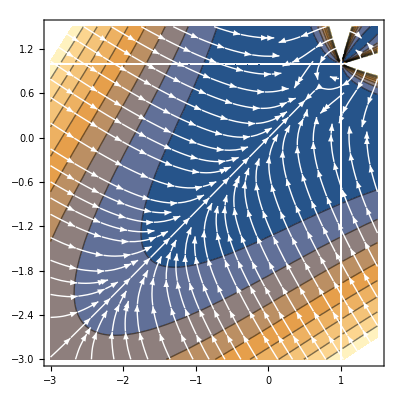

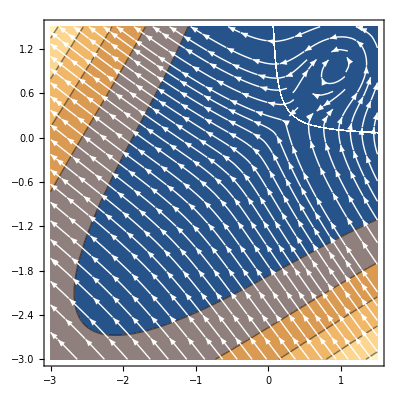

```mathematica
Show[{ContourPlot[ψGH[x,y,1,1,0.1][[1]],{x,-3,1.5},{y,-3,1.5}],
StreamPlot[-ψGH[x,y,1,1,0.1][[{2,3}]],{x,-3,1.5},{y,-3,1.5},VectorScale->{Automatic,Automatic,None},StreamStyle-> White]}]
Show[{
ContourPlot[InvertibleNeoHookeanPotential[x,y,1,1,0.1],{x,-3,1.5},{y,-3,1.5}],
StreamPlot[Eigenvectors[{{#4,#5},{#5,#6}}&@@ψGH[x,y,1,1,0.1]][[1]],{x,-3,1.5},{y,-3,1.5},StreamStyle-> White]
}]
```

```mathematica
ExtrapolatedNeoHookeanPotential[F_,λ_,μ_,ϵ_:0.3]:=Module[{px,py,u1,v1,v2,u2,σx,σy,ψ1,ψ2},
{u1,u2,σx,σy,v1,v2}=SVD2D[F];
ψGH[σx,σy,λ,μ,ϵ][[1]]
]
ExtrapolatedNeoHookeanStress[F_,λ_,μ_,ϵ_:0.3]:=Module[{px,py,u1,v1,v2,u2,σx,σy,ψ1,ψ2},
{u1,u2,σx,σy,v1,v2}=SVD2D[F];
{px,py}=ψGH[σx,σy,λ,μ,ϵ][[{2,3}]];
{{u1 v1 px-u2 v2 py,-u1 v2 px-u2 v1 py},{u2 v1 px+u1 v2 py,-u2 v2 px+u1 v1 py}}
]
ExtrapolatedNeoHookeanStressDifferential[F_,dF_,λ_,μ_,ϵ_:0.3]:=Module[{px,py,u1,v1,v2,u2,σx,σy,b11,b12,b21,b22,ψ11,ψ12,ψ1,ψ2,ψ22,ψ0,f1,f2},
{u1,u2,σx,σy,v1,v2}=SVD2D[F];
{ψ0,f1,f2,ψ11,ψ12,ψ22}=ψGHf[σx,σy,λ,μ,ϵ];
{{b11,b12},{b21,b22}}=({{u1, -u2}, {u2, u1}})ᵀ.dF.({{v1, -v2}, {v2, v1}})ᵀ;
(*({{u1, -u2}, {u2, u1}}).{{b11 ψ11+b22 ψ12,b21 ((-ψ1-ψ2)/(2 (σx+σy))+(ψ1-ψ2)/(2 (σx-σy)))+b12 ((ψ1-ψ2)/(2 (σx-σy))+(ψ1+ψ2)/(2 (σx+σy)))},{b12 ((-ψ1-ψ2)/(2 (σx+σy))+(ψ1-ψ2)/(2 (σx-σy)))+b21 ((ψ1-ψ2)/(2 (σx-σy))+(ψ1+ψ2)/(2 (σx+σy))),b11 ψ12+b22 ψ22}}.({{v1, -v2}, {v2, v1}})*)
({{u1, -u2}, {u2, u1}}).{{b11 ψ11+b22 ψ12,b21 f1+b12 f2},{b12 f1+b21 f2,b11 ψ12+b22 ψ22}}.({{v1, -v2}, {v2, v1}})
]
```

```mathematica
ff2==Apart[(σx ψ1-σy ψ2)/(σx^2-σy^2),{σx,σy}]
ff1==Apart[(σy ψ1-σx ψ2)/(σx^2-σy^2),{σx,σy}]
```

ff2=={(ψ1-ψ2)/(2 (σx-σy))+(ψ1+ψ2)/(2 (σx+σy)),(-ψ1+ψ2)/(2 (-σx+σy))+(ψ1+ψ2)/(2 (σx+σy))}

ff1=={(-ψ1-ψ2)/(2 (σx+σy))+(ψ1-ψ2)/(2 (σx-σy)),(-ψ1-ψ2)/(2 (σx+σy))+(-ψ1+ψ2)/(2 (-σx+σy))}

```mathematica
FEGradientFromElasticPotential[XX_,xx_,k_,ν_,pot_]:=Module[{xT,XT,x,X},
xT=Table[x[2i+j],{i,0,2},{j,1,2}];
XT=Table[X[2i+j],{i,0,2},{j,1,2}];
-W[XT]Table[D[pot[F[XT,xT],k,ν],x[i]],{i,1,6}]/.
{x[i_]:>  xx[[i]],X[i_]:>   XX[[i]]}
];
FEDifferentialFromElasticPotential[XX_,xx_,k_,ν_,pot_]:=Module[{xT,XT,x,X},
xT=Table[x[2i+j],{i,0,2},{j,1,2}];
XT=Table[X[2i+j],{i,0,2},{j,1,2}];
-W[XT]Table[D[pot[F[XT,xT],k,ν],x[i],x[j]],{i,1,6},{j,1,6}]/.{x[i_]:>  xx[[i]],X[i_]:>   XX[[i]]}
];

FEGradientFromStressTensor[XX_,xx_,k_,ν_,P_]:=Module[{xT,XT,x,X},
xT=Table[x[2i+j],{i,0,2},{j,1,2}];
XT=Table[X[2i+j],{i,0,2},{j,1,2}];
Flatten[ElasticForce[P[F[XT,xT],k,ν],XT]]/.{x[i_]:>  xx[[i]],X[i_]:>   XX[[i]]}
];

FEDifferentialFromStressTensor[XX_,xx_,k_,ν_,P_]:=Module[{fT,x,X,xT,XT,g},
xT=Table[x[2i+j],{i,0,2},{j,1,2}];
XT=Table[X[2i+j],{i,0,2},{j,1,2}];
g=Flatten[ElasticForce[P[F[XT,xT],k,ν],XT]];
Table[D[g[[i]],x[j]],{i,1,6},{j,1,6}]/.{x[i_]:>  xx[[i]],X[i_]:>   XX[[i]]}
]
FEDifferentialFromStressDifferentialTensor[XX_,xx_,k_,ν_,dP_]:=Module[{fT,x,X,xT,XT,g},
xT=Table[x[2i+j],{i,0,2},{j,1,2}];
XT=Table[X[2i+j],{i,0,2},{j,1,2}];
g=Flatten[ElasticForce[dP[F[XT,xT],F[XT,Partition[#,2]],k,ν],XT]]&;
MatrixComponents[g]/.{x[i_]:>  xx[[i]],X[i_]:>   XX[[i]]}
]

Block[{X,x},
X = {0,0,0,1,1,1};
x = {0.2,0.1,0.3,1.9,2.2,1.7};
{
FEGradientFromElasticPotential[X,x,1,1,NeoHookeanPotential],
FEGradientFromStressTensor[X,x,1,1,NeoHookeanStress],
FEGradientFromStressTensor[X,x,1,1,NeoHookeanStressSVD],
FEDifferentialFromElasticPotential[X,x,1,1,NeoHookeanPotential],
FEDifferentialFromStressTensor[X,x,1,1,NeoHookeanStress],
FEDifferentialFromStressTensor[X,x,1,1,NeoHookeanStressSVD],
FEDifferentialFromStressDifferentialTensor[X,x,1,1,NeoHookeanStressDifferentialSVD]
}
]//N//TableForm
```

0.0568451 | 0.965028 | 0.954761 | -1.06845 | -1.01161 | 0.103423
0.0568451 | 0.965028 | 0.954761 | -1.06845 | -1.01161 | 0.103423
0.0568451 | 0.965028 | 0.954761 | -1.06845 | -1.01161 | 0.103423
-0.501292
-0.0122753
0.489663
0.0471468
0.0116292
-0.0348716 | -0.0122753
-0.616615
-0.132428
0.622753
0.144703
-0.00613763 | 0.489663
-0.132428
-1.0827
0.103371
0.593033
0.029057 | 0.0471468
0.622753
0.103371
-1.12921
-0.150517
0.506461 | 0.0116292
0.144703
0.593033
-0.150517
-0.604663
0.00581459 | -0.0348716
-0.00613763
0.029057
0.506461
0.00581459
-0.500323
-0.501292
-0.0122753
0.489663
0.0471468
0.0116292
-0.0348716 | -0.0122753
-0.616615
-0.132428
0.622753
0.144703
-0.00613763 | 0.489663
-0.132428
-1.0827
0.103371
0.593033
0.029057 | 0.0471468
0.622753
0.103371
-1.12921
-0.150517
0.506461 | 0.0116292
0.144703
0.593033
-0.150517
-0.604663
0.00581459 | -0.0348716
-0.00613763
0.029057
0.506461
0.00581459
-0.500323
-0.501292
-0.0122753
0.489663
0.0471468
0.0116292
-0.0348716 | -0.0122753
-0.616615
-0.132428
0.622753
0.144703
-0.00613763 | 0.489663
-0.132428
-1.0827
0.103371
0.593033
0.029057 | 0.0471468
0.622753
0.103371
-1.12921
-0.150517
0.506461 | 0.0116292
0.144703
0.593033
-0.150517
-0.604663
0.00581459 | -0.0348716
-0.00613763
0.029057
0.506461
0.00581459
-0.500323
-0.501292
-0.0122753
0.489663
0.0471468
0.0116292
-0.0348716 | -0.0122753
-0.616615
-0.132428
0.622753
0.144703
-0.00613763 | 0.489663
-0.132428
-1.0827
0.103371
0.593033
0.029057 | 0.0471468
0.622753
0.103371
-1.12921
-0.150517
0.506461 | 0.0116292
0.144703
0.593033
-0.150517
-0.604663
0.00581459 | -0.0348716
-0.00613763
0.029057
0.506461
0.00581459
-0.500323

```mathematica
Block[{X,x},
X = {0,0,0,1,1,1};
x = {1.2,1.1,0.1,1.05,1.06,1.07};
{
FEGradientFromElasticPotential[X,x,1,1,ExtrapolatedNeoHookeanPotential],
FEGradientFromStressTensor[X,x,1,1,ExtrapolatedNeoHookeanStress],
FEDifferentialFromElasticPotential[X,x,1,1,ExtrapolatedNeoHookeanPotential],
FEDifferentialFromStressTensor[X,x,1,1,ExtrapolatedNeoHookeanStress],
FEDifferentialFromStressDifferentialTensor[X,x,1,1,ExtrapolatedNeoHookeanStressDifferential]
}
]//N//TableForm
```

-0.286071 | -7.95563 | 1.09329 | -1.12848 | -0.807224 | 9.08411
-0.286071 | -7.95563 | 1.09329 | -1.12848 | -0.807224 | 9.08411
-0.772198
1.04443
1.01352
-8.08956
-0.241322
7.04512 | 1.04443
-11.1414
7.06645
-1.21222
-8.11088
12.3537 | 1.01352
7.06645
-1.86416
-0.215486
0.850639
-6.85096 | -8.08956
-1.21222
-0.215486
-1.06732
8.30504
2.27955 | -0.241322
-8.11088
0.850639
8.30504
-0.609317
-0.194164 | 7.04512
12.3537
-6.85096
2.27955
-0.194164
-14.6332
-0.772198
1.04443
1.01352
-8.08956
-0.241322
7.04512 | 1.04443
-11.1414
7.06645
-1.21222
-8.11088
12.3537 | 1.01352
7.06645
-1.86416
-0.215486
0.850639
-6.85096 | -8.08956
-1.21222
-0.215486
-1.06732
8.30504
2.27955 | -0.241322
-8.11088
0.850639
8.30504
-0.609317
-0.194164 | 7.04512
12.3537
-6.85096
2.27955
-0.194164
-14.6332
-0.772198
1.04443
1.01352
-8.08956
-0.241322
7.04512 | 1.04443
-11.1414
7.06645
-1.21222
-8.11088
12.3537 | 1.01352
7.06645
-1.86416
-0.215486
0.850639
-6.85096 | -8.08956
-1.21222
-0.215486
-1.06732
8.30504
2.27955 | -0.241322
-8.11088
0.850639
8.30504
-0.609317
-0.194164 | 7.04512
12.3537
-6.85096
2.27955
-0.194164
-14.6332